```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2)-m(*p^2/(2m)*);Nx=25;max=100;
```

```mathematica
m =5/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.474;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ/π NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
Table[2NIntegrate[ϕ[2i+1][p]H[2n+1][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {6.34688}. NIntegrate obtained -0.000976982 and 1.0466×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {7.22579}. NIntegrate obtained -0.000721094 and 2.13554×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {8.59297}. NIntegrate obtained -0.000648988 and 1.3791×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{41070.5,{{1.86232,0.335593,-0.162478,-0.0116215,-0.0298395,-0.0100427,-0.0119764,-0.00662767,-0.00658319,-0.00455387,-0.00424951,-0.00329674,-0.00301269,-0.00249385,-0.00226863,-0.00195396,-0.00178127,-0.00157457,-0.00144219,-0.00129798,-0.00119549,-0.0010899,-0.00101004,-0.000929294,-0.000866382,-0.000799462},{0.360097,3.2539,0.552279,-0.242324,-0.00487031,-0.0428238,-0.010606,-0.0163402,-0.00772114,-0.00866075,-0.00548668,-0.00546414,-0.00402955,-0.00381994,-0.00306839,-0.00285162,-0.0024215,-0.00222656,-0.00194582,-0.00179582,-0.00160552,-0.00148259,-0.0013526,-0.00124567,-0.00115659,-0.00103525},{-0.16247,0.597031,4.34588,0.726964,-0.309431,0.00352953,-0.0542227,-0.0100038,-0.0200812,-0.00814659,-0.0103562,-0.00600285,-0.00640672,-0.00447902,-0.00442094,-0.00343682,-0.00327234,-0.00271111,-0.00254126,-0.00219038,-0.00204706,-0.0017971,-0.00170687,-0.00148988,-0.00116995,-0.00115575},{-0.0116215,-0.242302,0.791834,5.27681,0.87597,-0.36891,0.0122909,-0.0648111,-0.0088732,-0.0235766,-0.00824788,-0.0119107,-0.00631768,-0.00724649,-0.00479455,-0.00494118,-0.00370999,-0.00362738,-0.00294172,-0.00279713,-0.00239866,-0.00221281,-0.00159506,-0.000953834,-0.00150673,-0.00195631},{-0.0298395,-0.00487029,-0.30939,0.96093,6.10275,1.00733,-0.42295,0.0210258,-0.0748226,-0.00744749,-0.0269297,-0.00814869,-0.0133943,-0.00650562,-0.00803507,-0.00502633,-0.00541999,-0.00392356,-0.0039532,-0.00311672,-0.00306893,-0.00259006,-0.0020299,-0.000155175,-0.00293862,-0.00216139},{-0.0100427,-0.0428238,0.00352958,-0.368844,1.11237,6.85312,1.12566,-0.472813,0.0295897,-0.0843685,-0.00584261,-0.0301806,-0.00791169,-0.0148351,-0.0066034,-0.00879432,-0.00519841,-0.00587263,-0.00410497,-0.00423867,-0.00333541,-0.00341411,-0.000718551,-0.00368675,-0.00225076,-0.00177979},{-0.0119764,-0.010606,-0.0542227,0.012291,-0.422852,1.25079,7.54567,1.23388,-0.519326,0.0379272,-0.093517,-0.00412511,-0.0333485,-0.00757443,-0.0162461,-0.00663285,-0.00953517,-0.00532193,-0.00632154,-0.0042277,-0.00458382,-0.00263557,-0.0031867,-0.000610334,-0.00291906,-0.00364972},{-0.00662767,-0.0163402,-0.0100038,-0.0648111,0.021026,-0.472677,1.37911,8.19212,1.33399,-0.56307,0.046021,-0.102317,-0.00233642,-0.0364439,-0.00716161,-0.0176341,-0.00660861,-0.0102612,-0.00541837,-0.00673358,-0.00477072,-0.00421111,-0.00247408,-0.00232845,-0.00140565,-0.00958782},{-0.00658319,-0.00772114,-0.0200812,-0.0088732,-0.0748226,0.02959,-0.519147,1.49932,8.80066,1.42739,-0.604477,0.0538708,-0.110805,-0.000503731,-0.0394735,-0.00669053,-0.019003,-0.00653909,-0.0109842,-0.00547325,-0.00717394,-0.0047528,-0.0041804,-0.0000815357,0.00187757,-0.00862654},{-0.00455387,-0.00866075,-0.00814659,-0.0235766,-0.00744749,-0.0843685,0.0379276,-0.562842,1.61284,9.37731,1.51515,-0.643875,0.0614842,-0.119012,0.00135446,-0.0424419,-0.00617405,-0.0203548,-0.00643588,-0.011701,-0.00550361,-0.00919857,-0.0019192,-0.00264752,-0.000801748,-0.00495719},{-0.00424951,-0.00548668,-0.0103562,-0.00824788,-0.0269297,-0.00584261,-0.093517,0.0460216,-0.604193,1.72072,9.92665,1.59807,-0.681522,0.0688723,-0.126962,0.00322528,-0.0453531,-0.00562143,-0.0216902,-0.00630027,-0.012214,-0.00559918,-0.0108542,-0.00411868,-0.00604056,-0.00390989},{-0.00329674,-0.00546414,-0.00600285,-0.0119107,-0.00814868,-0.0301806,-0.00412511,-0.102317,0.0538716,-0.643529,1.82377,10.4522,1.67679,-0.717628,0.0760476,-0.134678,0.00509964,-0.0482094,-0.00504026,-0.02301,-0.00613613,-0.0121678,-0.00927525,-0.009763,-0.00594596,-0.00910642},{-0.00301269,-0.00402955,-0.00640672,-0.00631768,-0.0133943,-0.00791169,-0.0333485,-0.00233642,-0.110805,0.0614853,-0.681108,1.92263,10.9569,1.7518,-0.752362,0.0830224,-0.142178,0.00697069,-0.0510153,-0.00443667,-0.0243284,-0.00526279,-0.0150993,-0.0097289,-0.00933506,-0.00997557},{-0.00249385,-0.00381994,-0.00447901,-0.00724647,-0.0065056,-0.0148351,-0.00757443,-0.0364439,-0.000503737,-0.119012,0.0688738,-0.71714,2.0178,11.4431,1.82353,-0.785865,0.0898089,-0.149602,0.00883424,-0.0537746,-0.0038121,-0.0257138,-0.0031051,-0.0124067,-0.00631918,-0.010041},{-0.00226863,-0.00306839,-0.00442095,-0.00479456,-0.00803507,-0.0066034,-0.0162461,-0.00716161,-0.0394734,0.00135446,-0.126962,0.0760494,-0.751794,2.1097,11.9126,1.89231,-0.818257,0.0964189,-0.156594,0.0106866,-0.0565903,-0.00504833,-0.0278643,-0.00389836,-0.021629,-0.0063311},{-0.00195396,-0.00285161,-0.00343679,-0.00494114,-0.00502631,-0.00879433,-0.00663288,-0.0176341,-0.00669056,-0.042442,0.00322529,-0.134678,0.0830247,-0.78521,2.19867,12.367,1.95845,-0.849638,0.102864,-0.163536,0.0125283,-0.0584778,-0.00533832,-0.0293545,-0.00722169,-0.0110754},{-0.00178127,-0.00241145,-0.00327236,-0.00371001,-0.00541998,-0.00519831,-0.00953504,-0.00660844,-0.0190028,-0.00617394,-0.0453532,0.00509959,-0.142178,0.0898118,-0.817509,2.28499,12.8078,2.02217,-0.880095,0.109148,-0.170562,0.0158092,-0.0613581,-0.00330523,-0.0286253,-0.00595414},{-0.00157457,-0.00222657,-0.0027112,-0.00362771,-0.00392465,-0.00587475,-0.00532455,-0.0102631,-0.0065404,-0.0203545,-0.00562127,-0.0482101,0.00697081,-0.149479,0.0964222,-0.848791,2.36892,13.236,2.08369,-0.909703,0.115351,-0.17762,0.0168763,-0.0633813,-0.00427454,-0.0305843},{-0.00144218,-0.00194576,-0.00254085,-0.00293952,-0.0039485,-0.00409771,-0.00631415,-0.00541385,-0.0109817,-0.00643624,-0.0216904,-0.00503991,-0.0510156,0.00883417,-0.156593,0.102867,-0.879143,2.45066,13.6528,2.14319,-0.93852,0.120567,-0.184946,0.0232592,-0.0671862,-0.00460203},{-0.001298,-0.00179605,-0.00219163,-0.00280126,-0.00312479,-0.00424896,-0.0042395,-0.00674384,-0.00547308,-0.0116932,-0.00630194,-0.0230113,-0.00443557,-0.0537719,0.0106862,-0.163535,0.109155,-0.908641,2.53039,14.0589,2.20066,-0.965829,0.124578,-0.192058,0.025256,-0.0688518},{-0.00119543,-0.00160466,-0.00204181,-0.00238144,-0.00303214,-0.0032791,-0.00453512,-0.00435496,-0.00716597,-0.00550654,-0.0123987,-0.00614234,-0.0243181,-0.00381285,-0.0564811,0.0125244,-0.170313,0.115297,-0.937349,2.60827,14.4552,2.25673,-0.991419,0.129538,-0.196857,0.0283135},{-0.00109013,-0.00148495,-0.00180891,-0.00224272,-0.00253862,-0.00324643,-0.00341174,-0.00481272,-0.00444893,-0.00758232,-0.00551765,-0.013098,-0.00596105,-0.0256112,-0.00317538,-0.0591452,0.0143471,-0.176944,0.1213,-0.965329,2.68444,14.8399,2.31281,-1.01684,0.130808,-0.205732},{-0.00100955,-0.00134762,-0.00168357,-0.00196722,-0.00241705,-0.00267013,-0.00344611,-0.00352563,-0.00508659,-0.0045269,-0.00799667,-0.00550987,-0.0137937,-0.00575959,-0.0268898,-0.00252716,-0.0617693,0.0161535,-0.183428,0.127174,-0.992715,2.76132,15.2195,2.36604,-1.03926,0.137401},{-0.000929831,-0.00125174,-0.0015196,-0.00184475,-0.00210082,-0.00257955,-0.0027872,-0.00363837,-0.00362288,-0.00535835,-0.00459044,-0.00841405,-0.00548959,-0.0144867,-0.00554388,-0.0281561,-0.00186867,-0.0643489,0.0179389,-0.189778,0.132884,-1.01825,2.8354,15.5859,2.41941,-1.06249},{-0.000865463,-0.0011489,-0.00141609,-0.00165342,-0.00198655,-0.00222597,-0.00275316,-0.00292523,-0.00386586,-0.00374264,-0.00563854,-0.00464002,-0.00882377,-0.00544255,-0.0151679,-0.00531999,-0.0294061,-0.0011958,-0.0668882,0.0197021,-0.19601,0.138208,-1.04154,2.90487,15.94,2.4683},{-0.00080363,-0.00107204,-0.00129637,-0.00154961,-0.00176419,-0.00209796,-0.00228374,-0.00281668,-0.00296257,-0.00399983,-0.00376271,-0.00586905,-0.00463476,-0.00922042,-0.00539217,-0.0158335,-0.00505477,-0.0306551,-0.00059762,-0.0693934,0.0215791,-0.203285,0.142225,-1.06729,2.97856,16.2981}}}

{1.73534,2.9225,3.84675,4.63418,5.33343,5.97003,6.56147,7.1262,7.68523,8.25306,8.83775,9.43655,10.0512,10.6691,11.3103,11.954,12.6143,13.2733,13.9625,14.6554,15.3792,16.0975,16.9036,17.6356,18.6401,19.2743}

```mathematica
Table[2NIntegrate[ϕ[2i][p]H[2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {6.44454}. NIntegrate obtained -0.00305177 and 3.50668×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {6.44454}. NIntegrate obtained -0.00302668 and 3.63205×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {7.81172}. NIntegrate obtained -0.00387563 and 4.4206×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{8716.29,{{0.78887,0.1579,-0.140444,-0.0320552,-0.0368842,-0.0207532,-0.0193052,-0.0141762,-0.0127514,-0.010443,-0.00940059,-0.00812863,-0.00738043,-0.0065835,-0.00603548,-0.00549139},{0.172046,2.59176,0.438276,-0.214076,-0.0160829,-0.0428555,-0.0158318,-0.0188981,-0.0113717,-0.0113516,-0.00839882,-0.00792443,-0.00648326,-0.00601531,-0.00519625,-0.00481001},{-0.14044,0.472935,3.81688,0.637104,-0.282269,-0.00514151,-0.0524315,-0.0137122,-0.0212121,-0.0106528,-0.0119606,-0.00800234,-0.00800783,-0.00618243,-0.00591285,-0.00493363},{-0.0320552,-0.214062,0.691921,4.82206,0.799995,-0.343405,0.00490776,-0.0622428,-0.0118534,-0.0239954,-0.010187,-0.0129486,-0.00784939,-0.00838996,-0.00610354,-0.00605336},{-0.0368842,-0.0160829,-0.282239,0.874912,5.69733,0.940658,-0.399011,0.0144601,-0.071872,-0.00999812,-0.0269265,-0.00974963,-0.0140807,-0.00775125,-0.00888878,-0.00608888},{-0.0207532,-0.0428555,-0.00514147,-0.343352,1.03566,6.48363,1.06577,-0.450257,0.0236078,-0.0812222,-0.00810828,-0.029904,-0.0092891,-0.0152826,-0.00765663,-0.00944705},{-0.0193052,-0.0158318,-0.0524315,0.00490784,-0.39893,1.18085,7.2039,1.17921,-0.497975,0.0323927,-0.0902745,-0.00618629,-0.0328846,-0.00879372,-0.0165216,-0.00754837},{-0.0141762,-0.0188981,-0.0137122,-0.0622428,0.0144603,-0.450142,1.31438,7.87257,1.28348,-0.542771,0.0408451,-0.0990343,-0.0042425,-0.0358471,-0.00826345,-0.0177809},{-0.0127514,-0.0113717,-0.0212121,-0.0118534,-0.071872,0.023608,-0.497819,1.43876,8.49946,1.38031,-0.585102,0.0489929,-0.107517,-0.00228713,-0.0387799,-0.00770178},{-0.010443,-0.0113516,-0.0106528,-0.0239954,-0.00999812,-0.0812222,0.0323931,-0.542568,1.5557,9.09161,1.47095,-0.625315,0.0568588,-0.115738,-0.000328728,-0.0416768},{-0.00940059,-0.00839882,-0.0119606,-0.010187,-0.0269265,-0.00810824,-0.0902744,0.0408461,-0.584845,1.66646,9.65425,1.55634,-0.663691,0.0644649,-0.123717,0.00162605},{-0.00812863,-0.00792443,-0.00800234,-0.0129486,-0.00974963,-0.029904,-0.00618629,-0.0990343,0.0489936,-0.625001,1.77197,10.1914,1.63719,-0.700449,0.0718311,-0.131469},{-0.00738043,-0.00648326,-0.00800783,-0.00784939,-0.0140807,-0.0092891,-0.0328846,-0.0042425,-0.107517,0.0568597,-0.663311,1.87296,10.7064,1.71408,-0.735773,0.0789752},{-0.0065835,-0.00601531,-0.00618243,-0.00838996,-0.00775125,-0.0152826,-0.00879372,-0.0358471,-0.00228713,-0.115738,0.0644676,-0.699999,1.97,11.2016,1.78747,-0.769811},{-0.00603548,-0.00519626,-0.00591286,-0.00610356,-0.00888879,-0.00765662,-0.0165216,-0.00826345,-0.0387799,-0.000328726,-0.123717,0.0718328,-0.735245,2.06356,11.6792,1.85775},{-0.00549139,-0.00481001,-0.00493363,-0.00605336,-0.0060889,-0.00944708,-0.00754846,-0.017781,-0.0077018,-0.0416769,0.00162484,-0.131469,0.0789773,-0.7692,2.15401,12.1411}}}

{0.76162,2.3572,3.39755,4.24908,4.99778,5.70031,6.40832,7.14363,7.91324,8.70686,9.53567,10.3812,11.2838,12.1861,13.2475,14.1721}

{0.761624,2.35721,3.39752,4.2485,4.99223,5.6749,6.34253,7.02609,7.74136,8.47947,9.25297,10.0388,10.8833,11.7126,12.7155,13.532}

```mathematica
(1/{0.626739521734077,1.6277326243040982,2.327439934874855,2.9549791073801774,3.5044756698735355,4.0192253373739995,4.492895651252148,4.944467627623943,5.369445301782115,5.778545265759837,6.168533839196623,6.546297918526044,6.909427470600335,7.262715431794351,7.604306453266613,7.937722432349187,8.261496037218325,8.578319647507108,8.887006765148229,9.189678700266501,9.485358201680341,9.775756942919504,10.060057461226027,10.339667839552352,10.613895214180715,10.883916605160202,11.149138066869181,11.410556825450428,11.667658694481936,11.921298360859119,12.171026827085502,12.417583952483255})(Riffle[{0.7616201346457598,2.357204329606582,3.397549540842454,4.24908190350515,4.997775788813086,5.700308983031116,6.408320818398681,7.143630585595066,7.913240760945483,8.706856813176547,9.535665511453097,10.381220060338306,11.28379824556355,12.186096312128285,13.247541033613622,14.172102389735},{1.7353444606212767,2.9225002882308146,3.846907788652441,4.636335457885158,5.350087053457953,6.039389210658325,6.74578642777848,7.480690344332289,8.247458729967391,9.0364822386329,9.859138767474139,10.697769941495723,11.592916707724102,12.486294745892836,13.540572401585685,14.451333065938597}]-{0.626739521734077,1.6277326243040982,2.327439934874855,2.9549791073801774,3.5044756698735355,4.0192253373739995,4.492895651252148,4.944467627623943,5.369445301782115,5.778545265759837,6.168533839196623,6.546297918526044,6.909427470600335,7.262715431794351,7.604306453266613,7.937722432349187,8.261496037218325,8.578319647507108,8.887006765148229,9.189678700266501,9.485358201680341,9.775756942919504,10.060057461226027,10.339667839552352,10.613895214180715,10.883916605160202,11.149138066869181,11.410556825450428,11.667658694481936,11.921298360859119,12.171026827085502,12.417583952483255})
```

{0.21521,0.0661115,0.0127885,-0.0109912,-0.0305113,-0.0428733,-0.0542665,-0.0623186,-0.0692193,-0.0741464,-0.0759054,-0.0774344,-0.0725251,-0.0711757,-0.0605809,-0.0575772,-0.042154,-0.0385694,-0.0202712,-0.0166705,0.00530368,0.00852945,0.0319245,0.0346338,0.0631157,0.065142,0.0930079,0.0942757,0.135407,0.13583,0.164413,0.16378}

```mathematica
NIntegrate[ϕ[30][p]H[30][p],{p,-max,max},MaxRecursion->50]//Timing
```

{77.3281,28.2998}

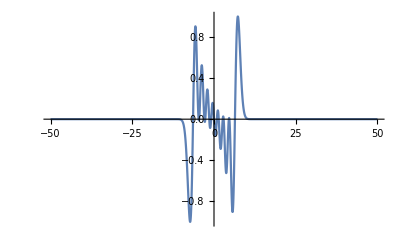

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-50,50},PlotRange->All]
```